```mathematica
scaling[future_, iguess_]:= Module[{children},
If[Length[future]==1,
Return[iguess];
];
nguess = scaling[future[[2;;]], iguess];

children = Table[future[[1]][[i]]->Table[,{j,}],{i,1,Length[future]}];
];
```

```mathematica
{1,2,3}[[2;;]]
```

{2,3}

```mathematica
Table[i,{i,0,2}]
```

{0,1,2}

```mathematica
d=1;
Manipulate[LogLogPlot[2^((2d)/δ^2(δ/(2d)Log[2,t]+(1+δ/(2d))^(-Log[2,t])-1)),{t,1,1000}],{δ,-1,1}]
```

```mathematica
∫_0^1 x^-x ⅆx//N
```

1.29129

```mathematica
N[∫_0^1 x^-x ⅆx,20]
```

1.2912859970626635404

```mathematica
1/√3//N
```

0.57735

```mathematica
√(3/5)//N
```

0.774597

```mathematica
5/9.
```

0.555556

```mathematica
8/9.
```

0.888889

```mathematica
∫_0^1 (x-√(3/5))^2 x^2(x+√(3/5))^2 ⅆx//N
```

0.0228571

```mathematica
g
```

boltzmann constant

WolframAlphaQueryResults

```mathematica
300*Log[3]*1.38065×10^-23
```

4.5504×10^-21

```mathematica
1/(1+E^(-300 Log[3]/230))//N
```

0.807364

```mathematica
Log[3]/50000//N
```

0.0000219722

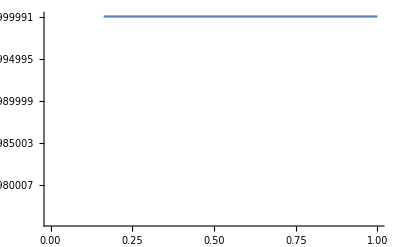

```mathematica
Plot[(1+190/100 E^(1/(1.38065×10^-23*300)f(190-100)*10^-9-6))/(1+E^(1/(1.38065×10^-23*300)f*(190-100)*10^-9-6)),{f,0,10*10^-12}]
```

```mathematica
(10*2π)/14.8
```

4.2454

```mathematica
4.2454*(100π)*10^-21
```

1.33373×10^-18

```mathematica
3*4.24/(14.8 10^3)(100π)^2
```

84.8252

```mathematica
10^3(100π)^2/(14.8*10^3)*10^-21
```

6.66865×10^-18

```mathematica
1.38065×10^-23*10^21
```

0.0138065

```mathematica
0.0138065*300*14.8*10^3/(16 π^2)
```

388.192

```mathematica
E//N
```

2.71828

```mathematica
700*.96*10^4/(4π)
```

534761.

```mathematica
euler[a_,b_,ya_,f_,n_]:=
(
h = (b-a)/n;
u = ya;
points={};
For[j=0,j<n,j++,
AppendTo[points,{a+j*h,u}];
u+=h*f[a+j*h,u];
];
Return[points];
)
```

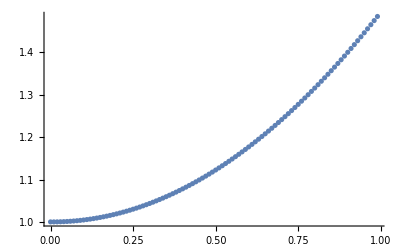

```mathematica
euler[0,4π,{1,0,0,1},#1&,100]
```

```mathematica
?AppendTo
```

AppendTo[s,elem] appends elem to the value of s, and resets s to the result.